## Initial setup

```mathematica
Remove["Global`*"]
```

```mathematica
e = 0.000001;
maxDepth = 3;
```

## Point sampling (current example)

```mathematica
npoints = 5;
sp = SpherePoints[npoints];
```

```mathematica
sn = sp;
```

```mathematica
Show[
Table[Graphics3D[Arrow[{sp[[i]], sp[[i]]+sn[[i]]}]],{i,npoints}],
ListPointPlot3D[sp, AspectRatio->1]
]
```

-Graphics3D-

## Octree spatial partition

```mathematica
initialWidth = Max[(Max@sp[[All,#]]&/@Range[3])-(Min@sp[[All,#]]&/@Range[3])] + 2.00 * e
```

2.

```mathematica
initialCenter = ((Max@sp[[All,#]]&/@Range[3])+(Min@sp[[All,#]]&/@Range[3]))/2.00
```

{0.,0.,0.25}

```mathematica
{xmin, ymin, zmin} = initialCenter - initialWidth * 0.65;
{xmax, ymax, zmax} = initialCenter + initialWidth * 0.65;
```

```mathematica
(* { {{center}, width}, {idx1, idx2, idx3, ...} } *)
octree = {{{initialCenter, initialWidth},Table[i, {i,Length[sp]}]}};
```

```mathematica
SubdivideNode[node_, pts_]:=Module[{n, points, idx, center, width, child1, child2, child3, child4, child5, child6, child7, child8, result},
n=node;
points=pts;
idx = n[[2]];
center = n[[1]][[1]];
width = n[[1]][[2]];
(* Subdivide only if the node has more than 1 points *)
If[Length[idx]>1,
(* True: Subdivide *)
child1 = {};
child2 = {};
child3 = {};
child4 = {};
child5 = {};
child6 = {};
child7 = {};
child8 = {};
Do[ (* for each point in the node *)
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child1 = Append[child1, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child2 = Append[child2, idx[[i]]]];
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child3 = Append[child3, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] ≤ center[[3]],child4 = Append[child4, idx[[i]]]];
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child5 = Append[child5, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] ≤ center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child6 = Append[child6, idx[[i]]]];
If[points[[idx[[i]]]][[1]] ≤ center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child7 = Append[child7, idx[[i]]]];
If[points[[idx[[i]]]][[1]] > center[[1]] && points[[idx[[i]]]][[2]] > center[[2]] && points[[idx[[i]]]][[3]] > center[[3]],child8 = Append[child8, idx[[i]]]]
,{i,Length[idx]}];
(* Construct what to return *)
result = {};
If[Length[child1]>0, result=Append[result,{{center+{-width/4.0, -width/4.0, -width/4.0}, width/2.0},child1}]];
If[Length[child2]>0, result=Append[result,{{center+{+width/4.0, -width/4.0, -width/4.0}, width/2.0},child2}]];
If[Length[child3]>0, result=Append[result,{{center+{-width/4.0, +width/4.0, -width/4.0}, width/2.0},child3}]];
If[Length[child4]>0, result=Append[result,{{center+{+width/4.0, +width/4.0, -width/4.0}, width/2.0},child4}]];
If[Length[child5]>0, result=Append[result,{{center+{-width/4.0, -width/4.0, +width/4.0}, width/2.0},child5}]];
If[Length[child6]>0, result=Append[result,{{center+{+width/4.0, -width/4.0, +width/4.0}, width/2.0},child6}]];
If[Length[child7]>0, result=Append[result,{{center+{-width/4.0, +width/4.0, +width/4.0}, width/2.0},child7}]];
If[Length[child8]>0, result=Append[result,{{center+{+width/4.0, +width/4.0, +width/4.0}, width/2.0},child8}]];
n = result;,
(* else *)
n = {n};
]; (* end if *)
n] (* end function *)
```

```mathematica
SubdivideOctree[oct_, pts_]:=Module[{tr, points, output, result},
tr=oct;
points=pts;
output = {};
Do[
result =SubdivideNode[tr[[i]],points];
 Do[output = Append[output,result[[j]]],{j,Length[result]}],
{i, Length[tr]}
];
output
]
```

```mathematica
octree
```

{{{{0.,0.,0.25},2.},{1,2,3,4,5}}}

```mathematica
Do[octree = SubdivideOctree[octree, sp], {i,maxDepth}]
```

```mathematica
nleaves = Length[octree]
```

5

## System

```mathematica
F[{x_,y_,z_}]:=If[Abs[x]<π/2 &&Abs[y]<π/2 && Abs[z]<π/2 ,( 2 π^(-3/2)*(Cos[x]*Cos[y]*Cos[z])),0.00]
```

```mathematica
(* F[q_]:=(2π)^(-3/2)*Exp[-1/2 qᵀ.q] *)
```

```mathematica
Fo[q_,c_,w_]:=F[1/w*(q-c)]
```

```mathematica
(* Gradient field *)
```

```mathematica
octree[[1]][[1]][[2]]
```

0.500001

```mathematica
V[q_]:=Sum[
Sum[
Fo[
q,
 octree[[i]][[1]][[1]], (* leaf i center *)
octree[[i]][[1]][[2]] (* leaf i width *)
]
 * sn[[  
octree[[i]][[2]][[j]]  (* j-th index of contents of leaf i *)
 ]],
{j, Length[ octree[[i]][[2]]]}], (* iterate over the contents of leaf i *)
{i,nleaves}] (* iterate over leaves *)
```

```mathematica
VectorPlot3D[V[{x,y,z}],{x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax}, VectorScaling-> Automatic]
```

-Graphics3D-

```mathematica
divV[{x_,y_,z_}]:=(V[{x+e, y, z}][[1]]-V[{x, y, z}][[1]])/e+(V[{x, y+e, z}][[2]]-V[{x, y, z}][[2]])/e+(V[{x, y, z+e}][[3]]-V[{x, y, z}][[3]])/e
```

```mathematica
Foxx[{x_,y_,z_}, c_, w_]:=(Fo[{x+e,y,z},c,w]-2.0*Fo[{x,y,z},c,w]+Fo[{x-e,y,z},c,w])/e^2
Foyy[{x_,y_,z_}, c_, w_]:=(Fo[{x,y+e,z},c,w]-2.0*Fo[{x,y,z},c,w]+Fo[{x,y-e,z},c,w])/e^2
Fozz[{x_,y_,z_}, c_, w_]:=(Fo[{x,y,z+e},c,w]-2.0*Fo[{x,y,z},c,w]+Fo[{x,y,z-e},c,w])/e^2
```

```mathematica
(* Div[V[{x,y,z}],{x,y,z}] *)
```

```mathematica
(* v =Table[NIntegrate[Div[V[{x,y,z}],{x,y,z}]*Fo[{x,y,z},oc[i],ow], {x,-Infinity,Infinity}, {y,-Infinity,Infinity}, {z,-Infinity,Infinity}],{i,npoints}] *)
```

```mathematica
v = Monitor[
Table[NIntegrate[divV[{x,y,z}]*Fo[{x,y,z}, octree[[i]][[1]][[1]],octree[[i]][[1]][[2]]], {x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax}, Method-> "GlobalAdaptive", AccuracyGoal->50],{i,nleaves}]
,
Row[{ProgressIndicator[i,{1,nleaves}],i}," "]]
```

{0.226015,0.256943,0.530092,0.541341,0.556407}

```mathematica
L=ParallelTable[
NIntegrate[Foxx[{x,y,z},octree[[i]][[1]][[1]],octree[[i]][[1]][[2]]] * Fo[{x,y,z},octree[[j]][[1]][[1]],octree[[j]][[1]][[2]]], {x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax},  Method-> "GlobalAdaptive", AccuracyGoal->50]+
NIntegrate[Foyy[{x,y,z},octree[[i]][[1]][[1]],octree[[i]][[1]][[2]]] * Fo[{x,y,z},octree[[j]][[1]][[1]],octree[[j]][[1]][[2]]], {x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax},  Method-> "GlobalAdaptive", AccuracyGoal->50]+
NIntegrate[Fozz[{x,y,z},octree[[i]][[1]][[1]],octree[[i]][[1]][[2]]] * Fo[{x,y,z},octree[[j]][[1]][[1]],octree[[j]][[1]][[2]]], {x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax}, Method-> "GlobalAdaptive", AccuracyGoal->50],
{i,nleaves},{j,nleaves}]
```

{{-0.580348,-0.0304981,-0.25217,-0.0416394,-0.0416413},{-0.0304965,-0.659743,-0.0199918,-0.242521,-0.242521},{-0.164058,-0.0199964,-0.886921,-0.2235,-0.223491},{-0.0171597,-0.191183,-0.2235,-0.886921,-0.223491},{-0.0171629,-0.191188,-0.22351,-0.22351,-0.886931}}

```mathematica
L = Re[L];
```

```mathematica
L//MatrixForm
```

(-0.580348 | -0.0304981 | -0.25217 | -0.0416394 | -0.0416413
-0.0304965 | -0.659743 | -0.0199918 | -0.242521 | -0.242521
-0.164058 | -0.0199964 | -0.886921 | -0.2235 | -0.223491
-0.0171597 | -0.191183 | -0.2235 | -0.886921 | -0.223491
-0.0171629 | -0.191188 | -0.22351 | -0.22351 | -0.886931)

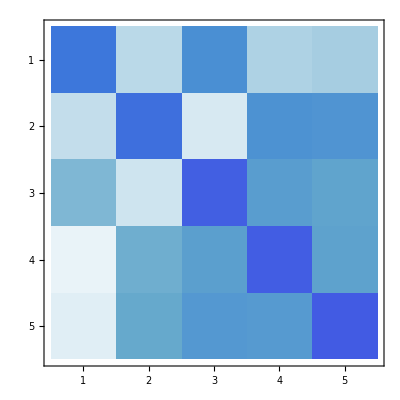

```mathematica
MatrixPlot[L]
```

```mathematica
xvec = LinearSolve[L,v]
```

{-0.17118,-0.0714051,-0.359263,-0.395697,-0.418383}

```mathematica
chi[q_]:=Sum[
xvec[[i]] * Fo[q,octree[[i]][[1]][[1]],octree[[i]][[1]][[2]]]
,{i,nleaves}]
```

```mathematica
γ = Mean[Table[chi[sp[[i]]],{i,npoints}]];
```

```mathematica
cp = ContourPlot3D[chi[{x,y,z}]==γ,{x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax},Mesh-> None,  ContourStyle-> {Green, Opacity[0.2]}];
```

```mathematica
Show[
cp,
ListPointPlot3D[sp, BoxRatios->1]
]
```

-Graphics3D-